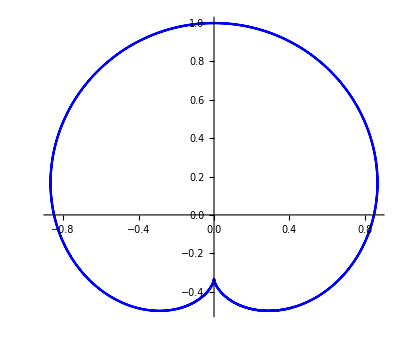

```mathematica
ClearAll["Global`*"];
F[x_,y_,t_]:=(y+1)Sin[Pi*t]-y*Sin[2Pi*t]+x*Cos[Pi*t]-x*Cos[2Pi*t];
Fd[x_,y_,t_]:= (y+1)Cos[Pi*t]-2y*Cos[2Pi*t]-x*Sin[Pi*t]+2x*Sin[2Pi*t];
parametricFunc[t_]:={x,y}/.(Solve[F[x,y,t]==0&&Fd[x,y,t]==0,{x,y}]);
ParametricPlot[parametricFunc[t],{t,E,E^2},PlotStyle->Blue]
```

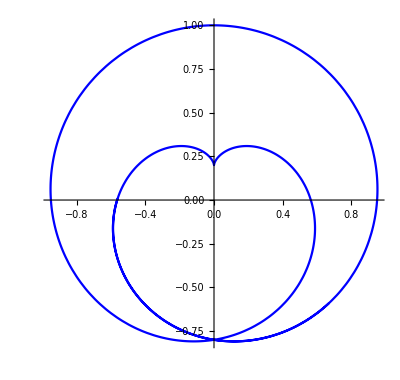

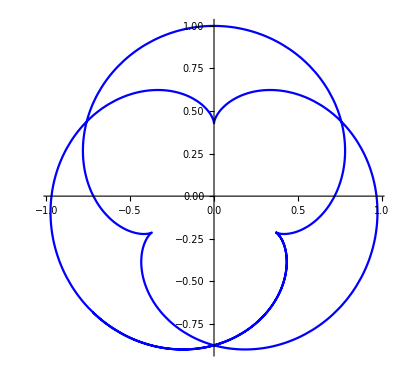

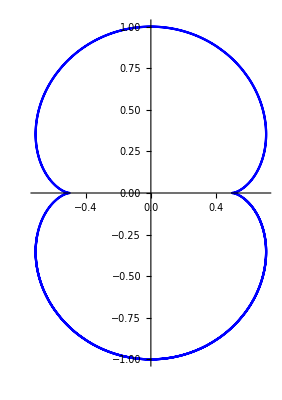

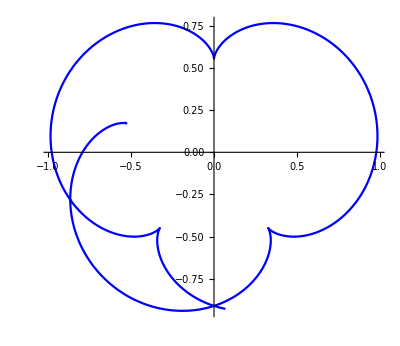

```mathematica
F[x_,y_,t_,a_]:=Sin[(a-2)Pi*t/2]+y*Sin[Pi*t]-y*Sin[a*Pi*t/2]+x*Cos[Pi*t]-x*Cos[a*Pi*t/2];
Fd[x_,y_,t_,a_]:= (a-2)Cos[(a-2)Pi*t/2]+2y*Cos[Pi*t]-a*y*Cos[a*Pi*t/2]-2x*Sin[Pi*t]+a*x*Sin[a*Pi*t/2];
parametricFunc[t_,a_]:={x,y}/.(Solve[F[x,y,t,a]==0&&Fd[x,y,t,a]==0,{x,y}]);
plot[a_,from_,to_]:=ParametricPlot[parametricFunc[t,a],{t,from,to},PlotStyle->Blue];
plot[3,E,E^2]
plot[5,E,E^2]
plot[6,E,E^2]
plot[7,E^9-E,E^9]
(*plot[17,E,E^2]*)
(*eqn2={F[x,y,t,a,k]==0,Fd[x,y,t,a,k]==0};
Print[FullSimplify[Eliminate[eqn2,t]]]*)
```